# Visualization aid

## RNA, LOCAL MOVES ON PLANE TREES, AND TRANSPOSITIONS ON TABLEAUX

Professor Julianna Tymoczko

Laura Seegerer, Jennifer Tripp, and Judy Wang

Mathematics Department
Smith College

Created by Judy Wang: 17 April 2014
Last modified Judy Wang: 11 June 2015

Mathematica 10.1.0 for Mac OS X x86 (64 bit)

## Functions

```mathematica
(* Load graph utilities for fancy orbit arrow options *)
<<GraphUtilities`
```

### Permuation groups

#### Functions that generate Weyl group C_n

This function outputs all the elements of C_n.

```mathematica
(* This function outputs all the elements of Subscript[C, n] in disjoint cycle notation. *)
Cn[n_]:=
Module[{length,bigList,list,test,cycles},
(* All permutations *)
length=2 n;
bigList=Permutations[Table[i,{i,length}],{length}];

(* Select only permutations whose entries are fully reflected to the other side of the mirror *)
list={};
For[ii=1,ii≤Length[bigList],ii++,
test=0;
For[j=1,j≤length/2,j++,
If[bigList[[ii]][[j]]+bigList[[ii]][[length-j+1]]==length+1,test++]];
If[test==length/2,list=Append[list,bigList[[ii]]]]];

(* Convert from 1-line notation into disjoint cycle notation *)
cycles={};
For[ii=1,ii≤Length[list],ii++,
AppendTo[cycles,PermutationCycles[list[[ii]]]]];
cycles]
```

This function outputs all the generators of C_n.

```mathematica
(* This function outputs the list of all the generators for Subscript[C, n] in the form of "{Cycles[{{1,2},{5,6}}],Cycles[{{2,3},{4,5}}],Cycles[{{3,4}}]}" in Subscript[C, 3]. *)
CnGenerators[n_]:=Table[If[i==n,Cycles[{{i,i+1}}],
Cycles[{{i,i+1},{2n-i,2n-i+1}}]],{i,n}];
```

#### Functions that generate Weyl group D_n

This function outputs all the elements of D_n.

```mathematica
(* This function outputs all the elements of Subscript[D, n] in disjoint cycle notation. *)
Dn[n_]:=

Module[{length,bigList,midList,list,test,cycles},
(* All permutations *)
length=2 n;
bigList=Permutations[Table[i,{i,length}],{length}];

(* Select only permutations whose entries are fully reflected to the other side of the mirror *)
midList={};
For[i=1,i<=Length[bigList],i++,
test=0;
For[j=1,j≤length/2,j++,
If[bigList[[i]][[j]]+bigList[[i]][[length-j+1]]==length+1,test++]];
If[test==length/2,midList=Append[midList,bigList[[i]]]]];

(* Select only the permutations who has an even number of entries with value greater than the mirror *)
list={};
For[i=1,i<=Length[midList],i++,
test=0;
For[j=1,j≤length/2,j++,
If[midList[[i]][[j]]>length/2,test++]]
If[Mod[test,2]==0,list=Append[list,midList[[i]]]]];

(* Convert from 1-line notation into disjoint cycle notation *)
cycles={};
For[ii=1,ii≤Length[list],ii++,
AppendTo[cycles,PermutationCycles[list[[ii]]]]];
cycles]
```

This function outputs all the generators of D_n.

```mathematica
(* This function outputs the list of all the generators for Subscript[D, n] in the form of "{Cycles[{{1,2},{5,6}}],Cycles[{{2,3},{4,5}}],Cycles[{{2,5},{3,4}}]}" in Subscript[D, 3]. *)
DnGenerators[n_]:=Table[If[i==n,Cycles[{{i,i+1},{i-1,i+2}}],
Cycles[{{i,i+1},{2n-i,2n-i+1}}]],{i,n}];
```

### Trees

#### Convert a Young Diagram into a tree

This function converts a Young Diagram into a plane tree.

```mathematica
(* This function converts a Young Diagram into a graphical tree. *)
YDTree[yd_]:=Module[{toprow,start,end,ydlength,diff,iList,jList,masterList,newi,newj,iLast,jLast,masterLast,edge,tempList},
toprow=yd[[1]]; (* Top row of the Young diagram *)
start=1; (* Array position of the starting vertex of a directed edge *)
end=2;  (* Array position of the ending vertex of a directed edge *)
ydlength=Length[toprow]; (* Length of Young diagram *)
iList={1->2}; (* List of downward edges *)
jList={}; (* List of upward edges *)
masterList=iList; (* List of both doward and upward edges *)

For[ii=1,ii<ydlength,ii++,
diff=toprow[[ii+1]]-toprow[[ii]]; (* Difference between an entry in the top row and the next entry in the top row *)
(* If diff == 1 *)
If[diff==1,
iLast=Last[iList];
newi=iLast[[end]]-> iLast[[end]]+1;
AppendTo[iList,newi];
AppendTo[masterList,newi],
(* If diff ≠ 1 *)
(* Search for the first element in masterList whose end point is greater than start point, then reverse the start and end points *)
edge=Last[masterList];
newj=edge[[end]]->edge[[start]];
tempList={newj};
For[jj=1,jj≤Length[masterList],jj++,
If[Length[tempList]==diff-1,Break[]];
edge=masterList[[-jj]];
If[edge[[end]]>edge[[start]]&&edge[[end]]==newj[[end]],
newj=edge[[end]]->edge[[start]];
AppendTo[tempList,newj]]];
jList=Join[jList,tempList];
masterList=Join[masterList,tempList];
newi=Last[jList][[end]]-> Last[iList][[end]]+1; (* One downward half edge *)
AppendTo[iList,newi];
AppendTo[masterList,newi]]];
(* Calculate the last j-edges *)
diff=ydlength-Last[toprow];
edge=Last[masterList];
newj=edge[[end]]->edge[[start]];
tempList={newj};
For[jj=1,jj≤Length[masterList],jj++,
If[Length[tempList]==diff-1,Break[]];
edge=masterList[[-jj]];
If[edge[[end]]>edge[[start]]&&edge[[end]]==newj[[end]],
newj=edge[[end]]->edge[[start]];
AppendTo[tempList,newj]]];
jList=Join[jList,tempList];
masterList=Join[masterList,tempList];
(* AppendTo[jList,Last[jList]]; *)
Show[TreePlot[iList,Automatic,1,DirectedEdges->True,VertexLabeling->False,PlotStyle->PointSize[Large]],ImageSize->30]];
YDTree[{{1,2,4,5,7,11,12,15,16,18,19,21,25},{3,6,8,9,10,13,17,20,22,23,24,26}}] ;
YDTree[{{1,2,3,5,9},{4,6,7,8,10}}];
YDTree[{{1,2,4,7},{3,5,6,8}}];
YDTree[{{1,3,4,6},{2,5,7,8}}] ;
```

#### Display trees with Young Diagrams

This function displays trees with Young Diagrams.

```mathematica
(* This function displays trees with Young Diagrams. *)
YDTdisplay[yd_]:=Module[{table,tree},
table=Grid[yd,Frame->All];
tree=YDTree[yd];
Grid[{{tree},{table}},ItemSize->{{10,3}},Spacings->{0,0.5},Frame->False]];
YDTdisplay[{{1,2,3},{4,5,6}}];
```

This function displays trees with Young Diagrams as well as the permutation applied.

```mathematica
(* This function displays trees with Young Diagrams as well as the permutation applied. *)
YDTPdisplay[yd_,perm_]:=Module[{table,tree},
table=Grid[yd,Frame->All];
tree=YDTree[yd];
Grid[{{tree},{table},{perm[[1]]}},ItemSize->{{10,3,3}},Spacings->{1,1},Frame->True]];
```

### Operations on Young Diagrams

#### Handy internal functions

```mathematica
(* For each entry in a cycle, this function finds the element in the input list that matches the entry, and outputs the cycle in the from of list positions. *)
indexForm[list_,cycle_]:=Module[{newcycle},
newcycle={};
For[ii=1,ii≤Length[cycle],ii++,
For[j=1,j≤Length[list],j++,
If[cycle[[ii]]==list[[j]],AppendTo[newcycle,j]]]];
Cycles[{newcycle}]]
```

```mathematica
(* This function rearranges a table into a Young Diagram. *)
rearrange[yd_]:=Module[{height,length,ydrow,ydTrans,ydcol},
height=Length[yd];
length=Length[yd[[1]]];
ydrow=Table[Sort[yd[[i]]],{i,height}]; (* Orders all the rows *)
ydTrans=Transpose[ydrow];
ydcol=Table[Sort[ydTrans[[i]]],{i,length}]; (* Orders all the rows *)
ydnew=Transpose[ydcol]]
```

#### Generating Young Diagrams

This function generates all possible n×m Young Diagrams.

```mathematica
(* This function generates all possible n×m Young Diagrams, where n is width and m is height. *)
YoungTableaux[n_,m_]:=Module[{allperm,allpartperm,YDall},
allperm=Permutations[Table[i,{i,n*m}]];
allpartperm=Table[Partition[allperm[[i]],n],{i,(n*m)!}];
YDall=Table[rearrange[allpartperm[[i]]],{i,(n*m)!}] ;
DeleteDuplicates[YDall]]
```

### Orbits

#### Applying permutations to a Young Diagram

```mathematica
(* This function applies a permuation to a Young Diagram. The parameter perm_ takes the form of "Cycles[{{a, b},{c, d},{e, f, g}}]." *)
YDPerm[yd_,perm_]:=Module[{newList,cycles},
(* Number of cycles in a permutation *)
cycles=Length[perm[[1]]]; 
newList=Flatten[yd];
(* Applies permutation to list *)
For[k=1,k≤cycles,k++,
newList=Permute[newList,indexForm[newList,perm[[1]][[k]]]]]; 
newList=Partition[newList,Length[yd[[1]]]];
rearrange[newList] ];
```

#### Finding one orbit

This functions takes a Young diagram and a group of permutations and outputs the orbit that the Young diagram is in.

```mathematica
(* This function finds a single orbit *)
findOrbit[yd_,permutations_]:=Module[{parent, parents,child,children,childless,orbit},
parent=yd;
parents={};
child={};
children={};
childless=False;
orbit={};

While[!childless,
AppendTo[parents,parent];
For[qq=1,qq≤ Length[permutations],qq++,
child=YDPerm[parent,permutations[[qq]]];
AppendTo[orbit,{YDTdisplay[parent]->YDTdisplay[child],StandardForm[permutations[[qq]][[1]]]}];
AppendTo[children,child];
];
children=DeleteDuplicates[children];
children=Complement[children,parents];  (* Removes from children anything that is in parents *)
If[children=={},childless=True,parent=children[[1]]];
];

LayeredGraphPlot[orbit,
Top,
PlotRangePadding->None,
VertexLabeling->True,
SelfLoopStyle->All,
PackingMethod->"ClosestPacking",
AspectRatio->Automatic,
ImageSize->500,
EdgeRenderingFunction->
({Arrow[#1,.25],
Text[#3,LineScaledCoordinate[#1,.5],
Background->White]}&)]];
(* Test inputs: *)
(* findOrbit[{{1,2,3},{4,5,6}},CnGenerators[3]] *)
(* findOrbit[{{1,2,3,4},{5,6,7,8}},CnGenerators[4]] *)
(* findOrbit[{{1,2,3,4,5},{6,7,8,9,10}},CnGenerators[5]] *)
(* findOrbit[{{1,2,3,4,8},{5,6,7,9,10}},CnGenerators[5]] *)
(* findOrbit[{{1,2,5,6,8},{3,4,7,9,10}},CnGenerators[5]] *)
```

#### Finding all orbits

This function finds all the orbits of a group.

```mathematica
(* This function finds all the orbits of a group. *)
findOrbits[YoungTableaux_,permutations_]:=Module[{n,masterList,parent,parents,child,children,childless,orbit, orbits},
n=Length[permutations];
masterList=YoungTableaux;
orbits={};

(* Find all orbits *)
While[masterList≠{},
parent=masterList[[1]];
parents={};
child={};
children={};
childless=False;
orbit={};

(* Find one orbit *)
While[!childless,
AppendTo[parents,parent];
For[qq=1,qq≤ Length[permutations],qq++,
child=YDPerm[parent,permutations[[qq]]];
AppendTo[orbit,{YDTdisplay[parent]->YDTdisplay[child],StandardForm[permutations[[qq]][[1]]]}];
AppendTo[children,child];
];
children=DeleteDuplicates[children];
children=Complement[children,parents];  (* Removes from children anything that is in parents *)
If[children=={},childless=True,parent=children[[1]]];
]; (* End of inner while loop *)
masterList= Complement[masterList,parents];
orbits=Catenate[{orbit,orbits}];
]; (* End of outer while loop *)
Print[LayeredGraphPlot[orbits,
Top,
PlotRangePadding->None,
VertexLabeling->True,
SelfLoopStyle->All,
AspectRatio->Automatic,
Background->White,
BaseStyle->{FontWeight->"Bold"},
PackingMethod->"ClosestPacking",
ImageSize->1635.7314097871797+3971.016177219348/n^3-2928.3796302592777/n^2-2471.2119092411535/n+67.24545695837797 n-104.0783880112127 n^2+29.676883546736757 n^3,
EdgeRenderingFunction->
({Arrowheads[-0.6208958013100486-1.5602253420319105/n^3+1.2099738632843346/n^2+1.0787120082456376/n-0.026416028141285186 n+0.04972596105586764 n^2-0.005874661102595701 n^3],
Arrow[#1,-0.12379123008990175-0.8565364532663182/n^3+0.4154891410095351/n^2+0.5609419146415267/n+0.014373551555270167 n+0.02210416703365013 n^2-0.002581090883762067 n^3],
Text[#3,LineScaledCoordinate[#1,.475],
Background->White]}&)]]];
```

## Output scaling

### ImageSize

1635.73+3971.02/n^3-2928.38/n^2-2471.21/n+67.2455 n-104.078 n^2+29.6769 n^3

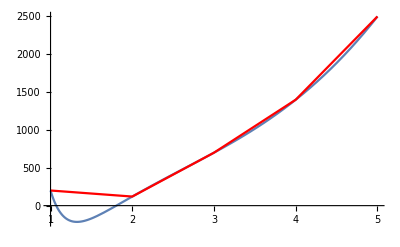

```mathematica
(* ImageSize *)
Clear[n];
p1=200;
p2=120;
p3=700;
p4=1400;
p5=2500;
dataline=ListLinePlot[{p1,p2,p3,p4,p5},AxesLabel->Automatic,PlotStyle->Red];
data={{1,p1},{2,p2},{3,p3},{4,p4},{5,p5}};
fitline=Fit[data,{1/n^3,1/n^2,1/n,1,n,n^2,n^3},n]
Show[Plot[fitline,{n,1,5}],dataline]
```

#### ImageSize

```mathematica
(* ImageSize *)
Clear[n];
p1=200;
p2=120;
p3=700;
p4=1400;
p5=2500;
dataline=ListLinePlot[{p1,p2,p3,p4,p5},AxesLabel->Automatic,PlotStyle->Red];
data={{1,p1},{2,p2},{3,p3},{4,p4},{5,p5}};
fitline=Fit[data,{1/n^3,1/n^2,1/n,1,n,n^2,n^3},n]
Show[Plot[fitline,{n,1,5}],dataline]
```

1635.73+3971.02/n^3-2928.38/n^2-2471.21/n+67.2455 n-104.078 n^2+29.6769 n^3

-Graphics-

### Arrowheads

-0.620896-1.56023/n^3+1.20997/n^2+1.07871/n-0.026416 n+0.049726 n^2-0.00587466 n^3

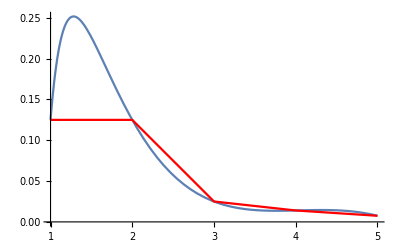

```mathematica
(* Arrowheads *)
Clear[n];
p1=0.125;
p2=0.125;
p3=0.025;
p4=0.014;
p5=0.0075;
dataline=ListLinePlot[{p1,p2,p3,p4,p5},AxesLabel->Automatic,PlotStyle->Red];
data={{1,p1},{2,p2},{3,p3},{4,p4},{5,p5}};
fitline=Fit[data,{1/n^3,1/n^2,1/n,1,n,n^2,n^3},n]
Show[Plot[fitline,{n,1,5}],dataline]
```

### Arrow

-0.123791-0.856536/n^3+0.415489/n^2+0.560942/n+0.0143736 n+0.0221042 n^2-0.00258109 n^3

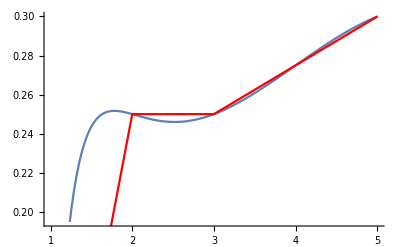

```mathematica
(* Arrow *)
Clear[n];
p1=0.03;
p2=0.25;
p3=0.25;
p4=0.275;
p5=0.3;
dataline=ListLinePlot[{p1,p2,p3,p4,p5},AxesLabel->Automatic,PlotStyle->Red];
data={{1,p1},{2,p2},{3,p3},{4,p4},{5,p5}};
fitline=Fit[data,{1/n^3,1/n^2,1/n,1,n,n^2,n^3},n]
Show[Plot[fitline,{n,1,5}],dataline]
```

## Applying C_n to Young Diagrams

### Orbits in C_1

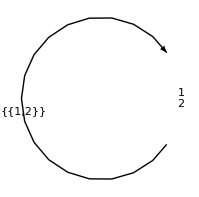

{0.084986,Null}

```mathematica
n=1; Timing[findOrbits[YoungTableaux[n,2],CnGenerators[n]]]
```

### Orbits in C_2

```mathematica
n=2; Timing[findOrbits[YoungTableaux[n,2],CnGenerators[n]]]
```

-Graphics-

{0.097173,Null}

### Orbits in C_3

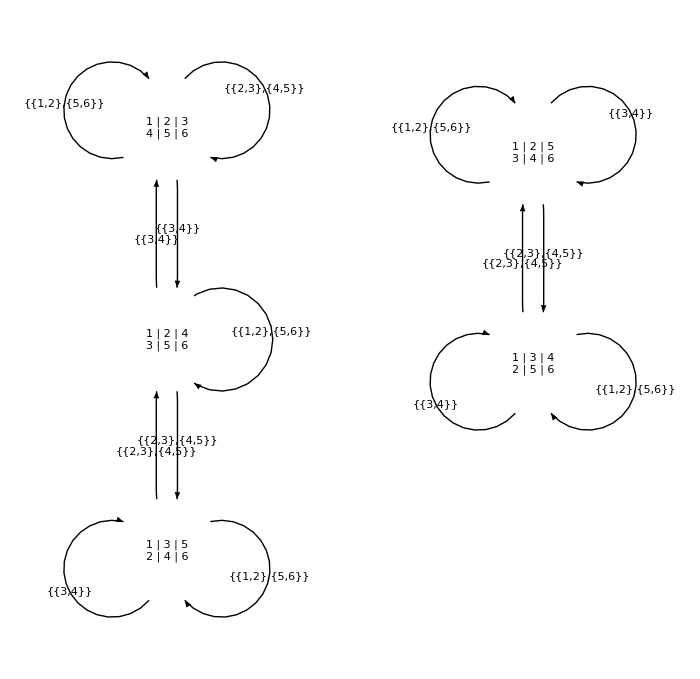

{0.36177,Null}

```mathematica
n=3; Timing[findOrbits[YoungTableaux[n,2],CnGenerators[n]]]
```

### Orbits in C_4

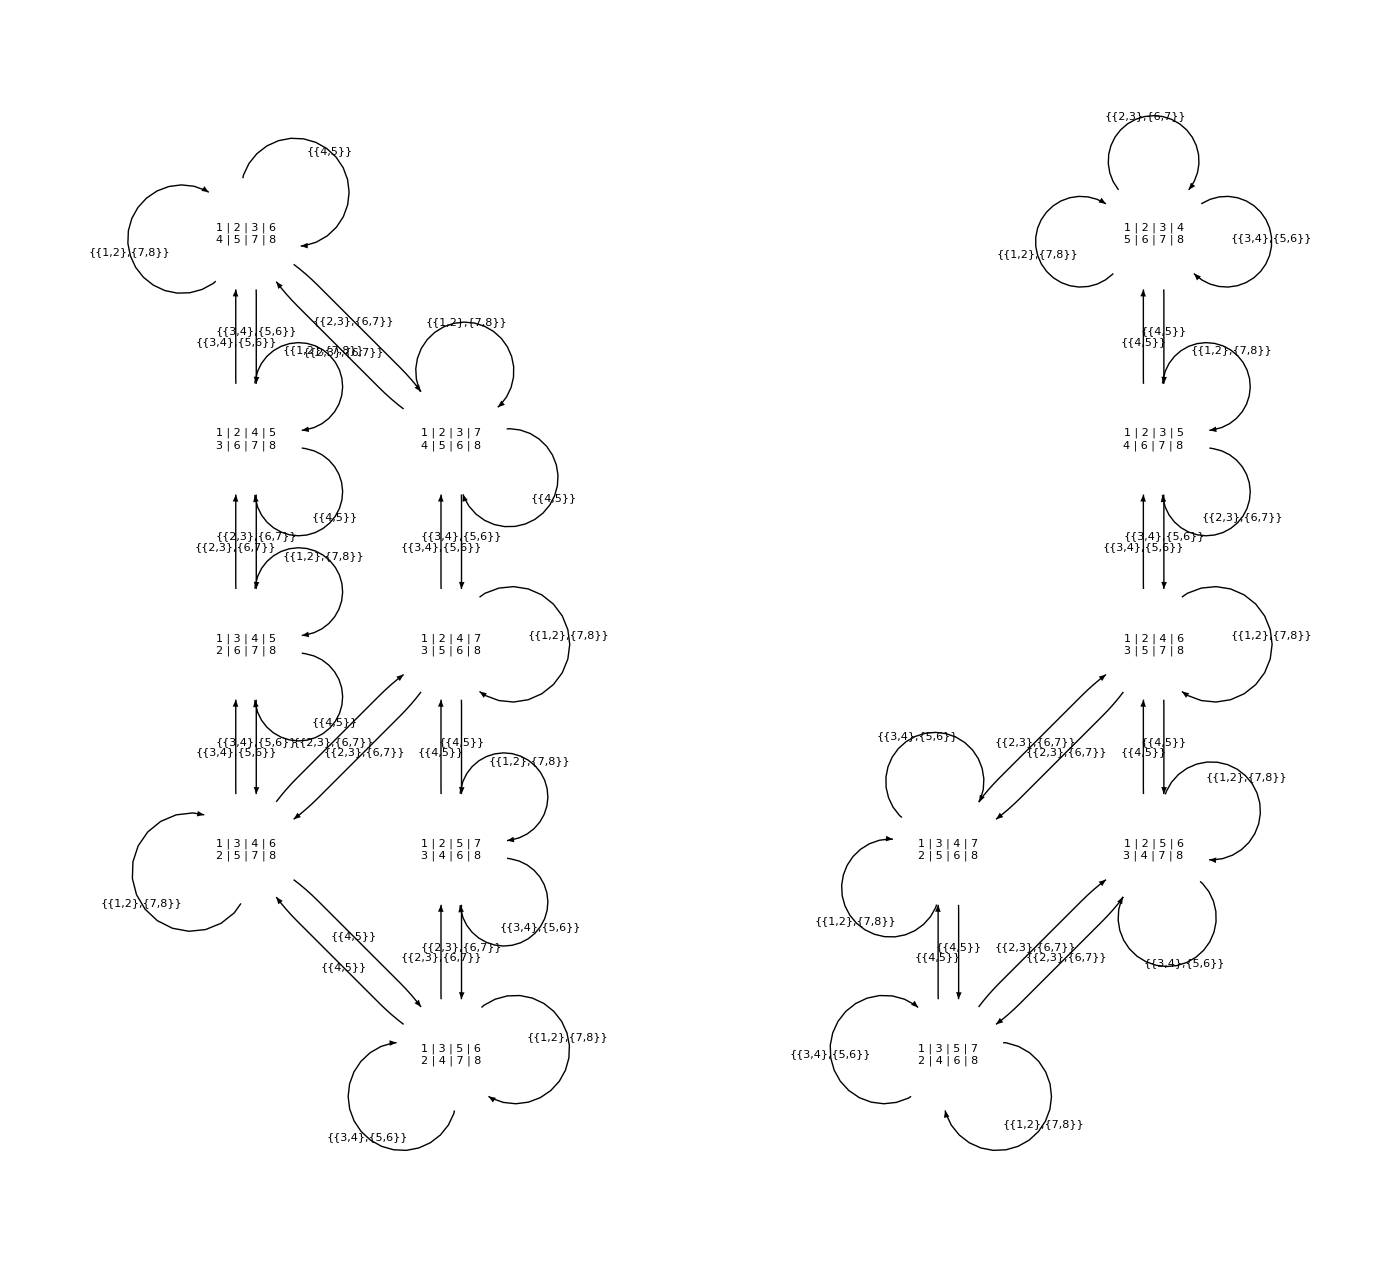

{3.84622,Null}

```mathematica
n=4; Timing[findOrbits[YoungTableaux[n,2],CnGenerators[n]]]
```

### Orbits in C_5

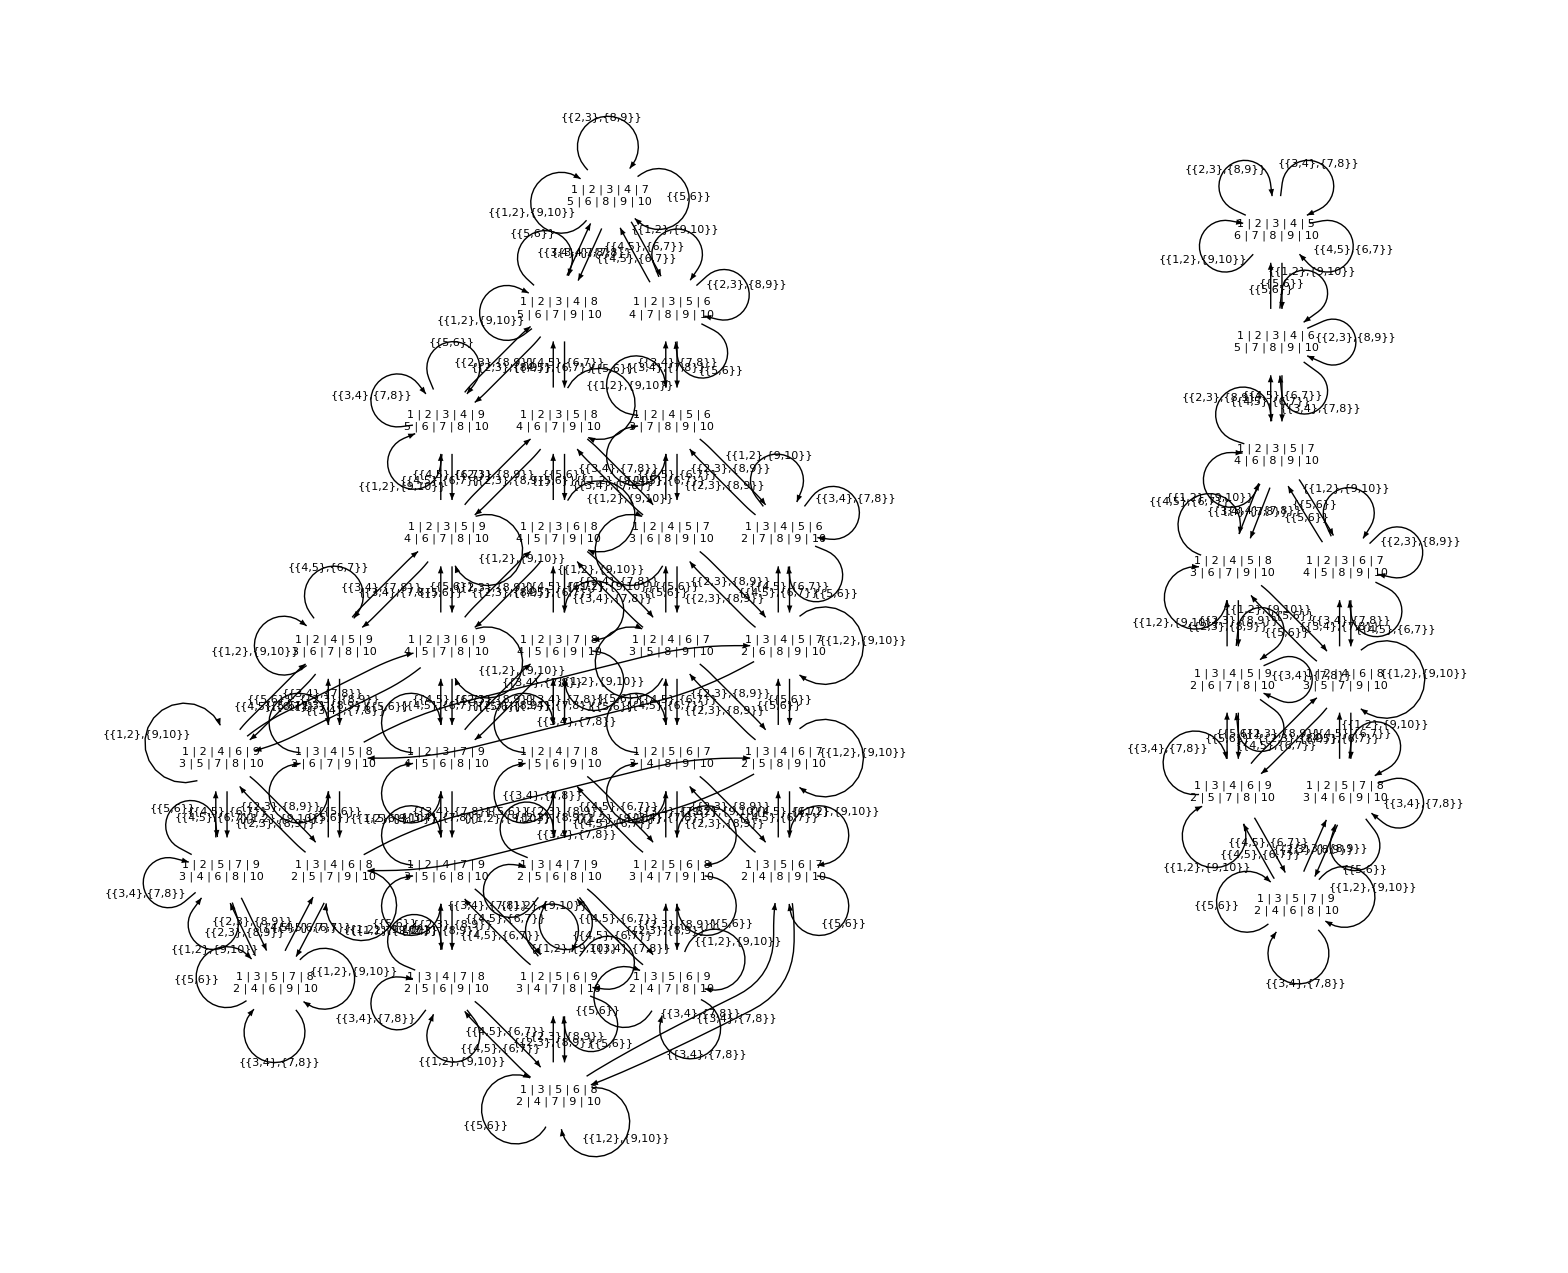

{257.013,Null}

```mathematica
n=5; Timing[findOrbits[YoungTableaux[n,2],CnGenerators[n]]]
```

## Applying D_n to Young Diagrams

### Non-orbits in D_3

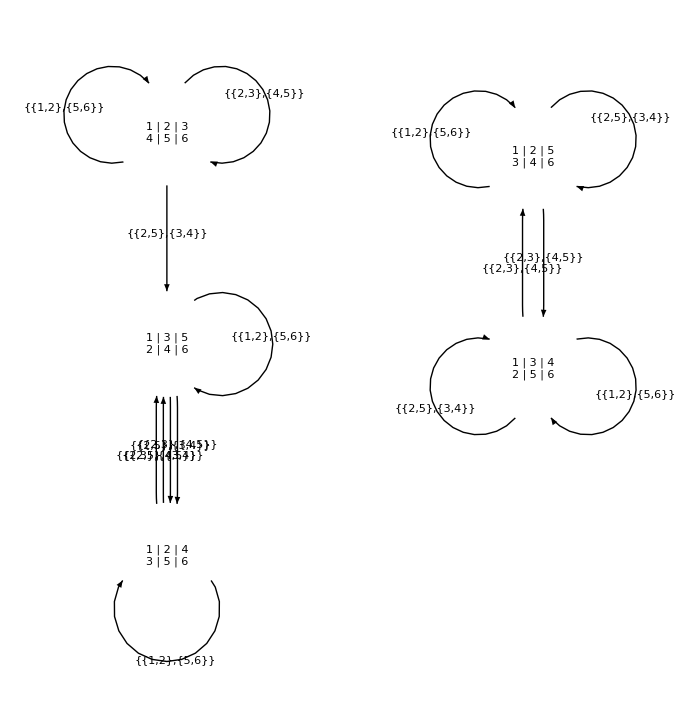

{0.363351,Null}

```mathematica
n=3; Timing[findOrbits[YoungTableaux[n,2],DnGenerators[n]]]
```

### Non-orbits in D_4

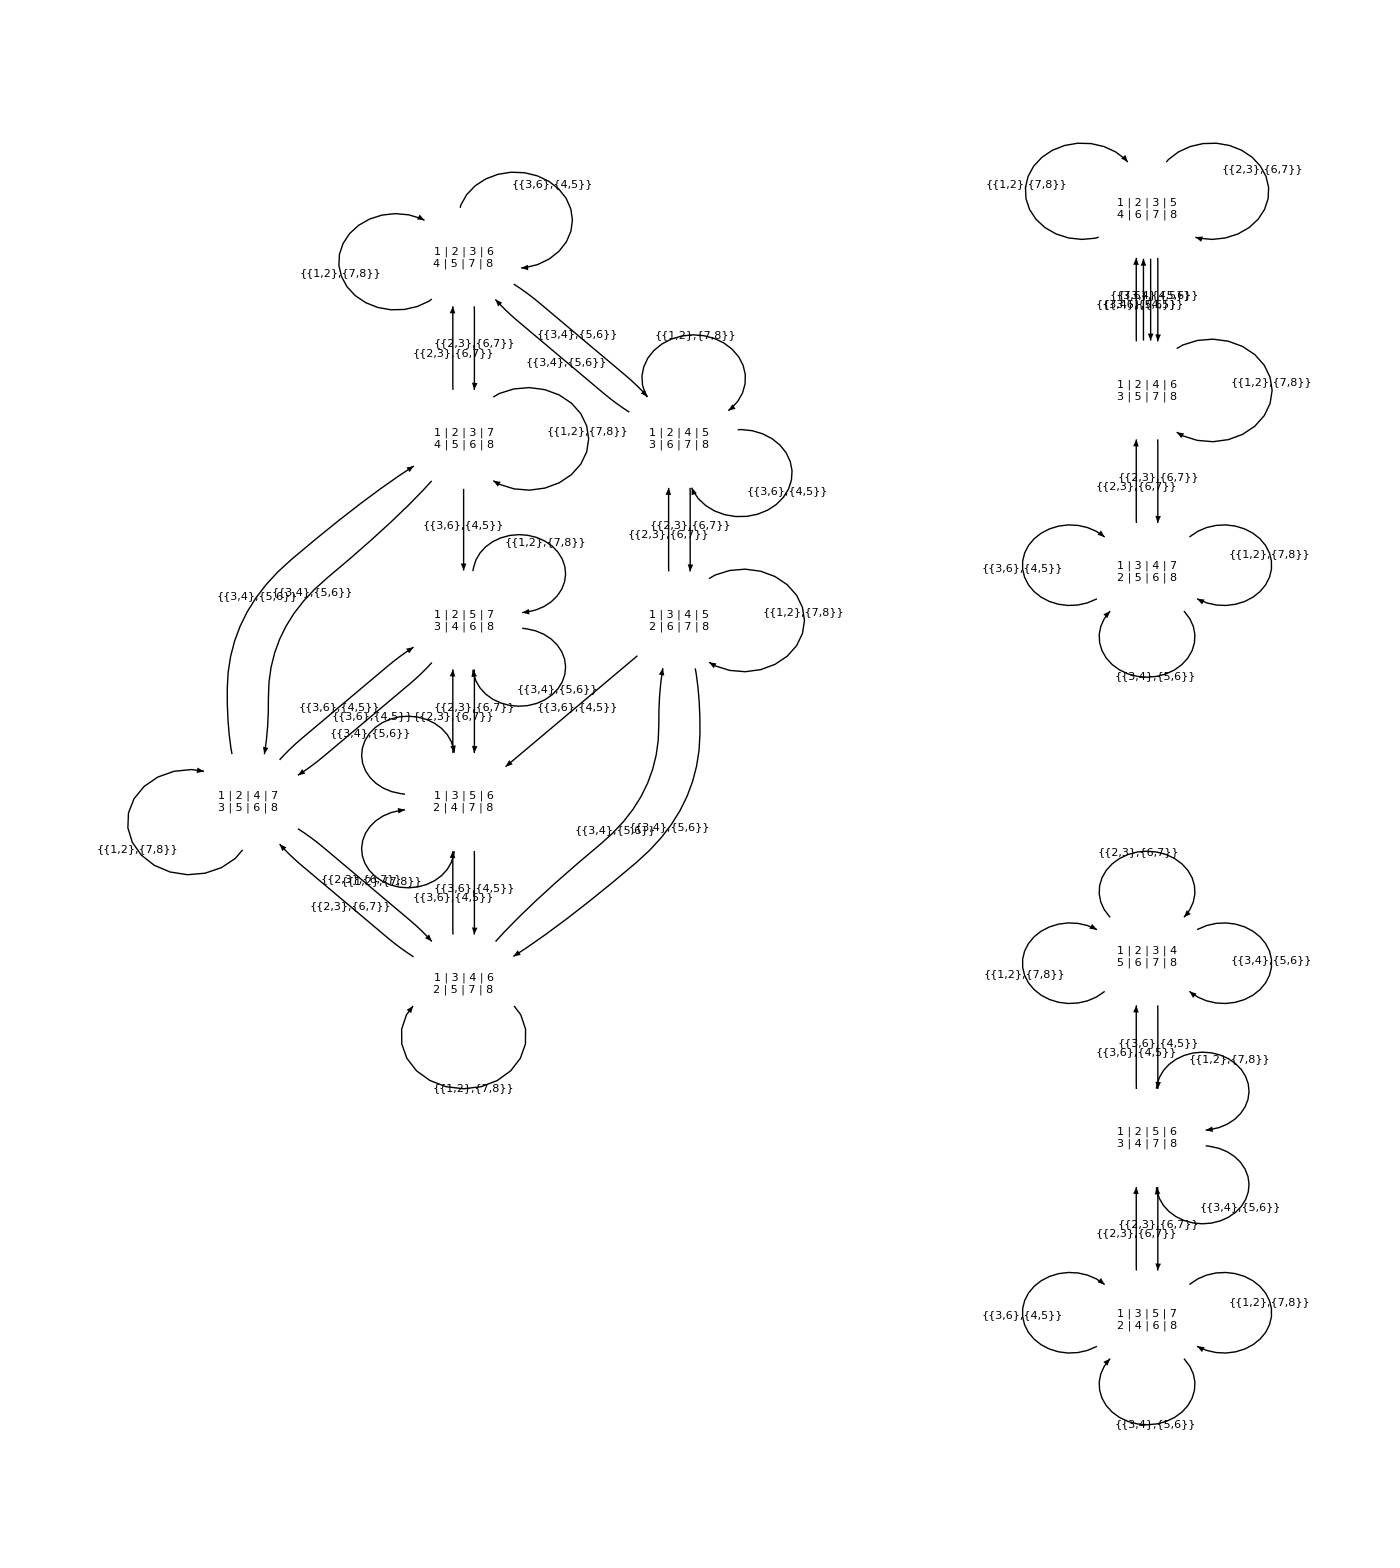

{3.61338,Null}

```mathematica
n=4; Timing[findOrbits[YoungTableaux[n,2],DnGenerators[n]]]
```

### Non-orbits in D_5

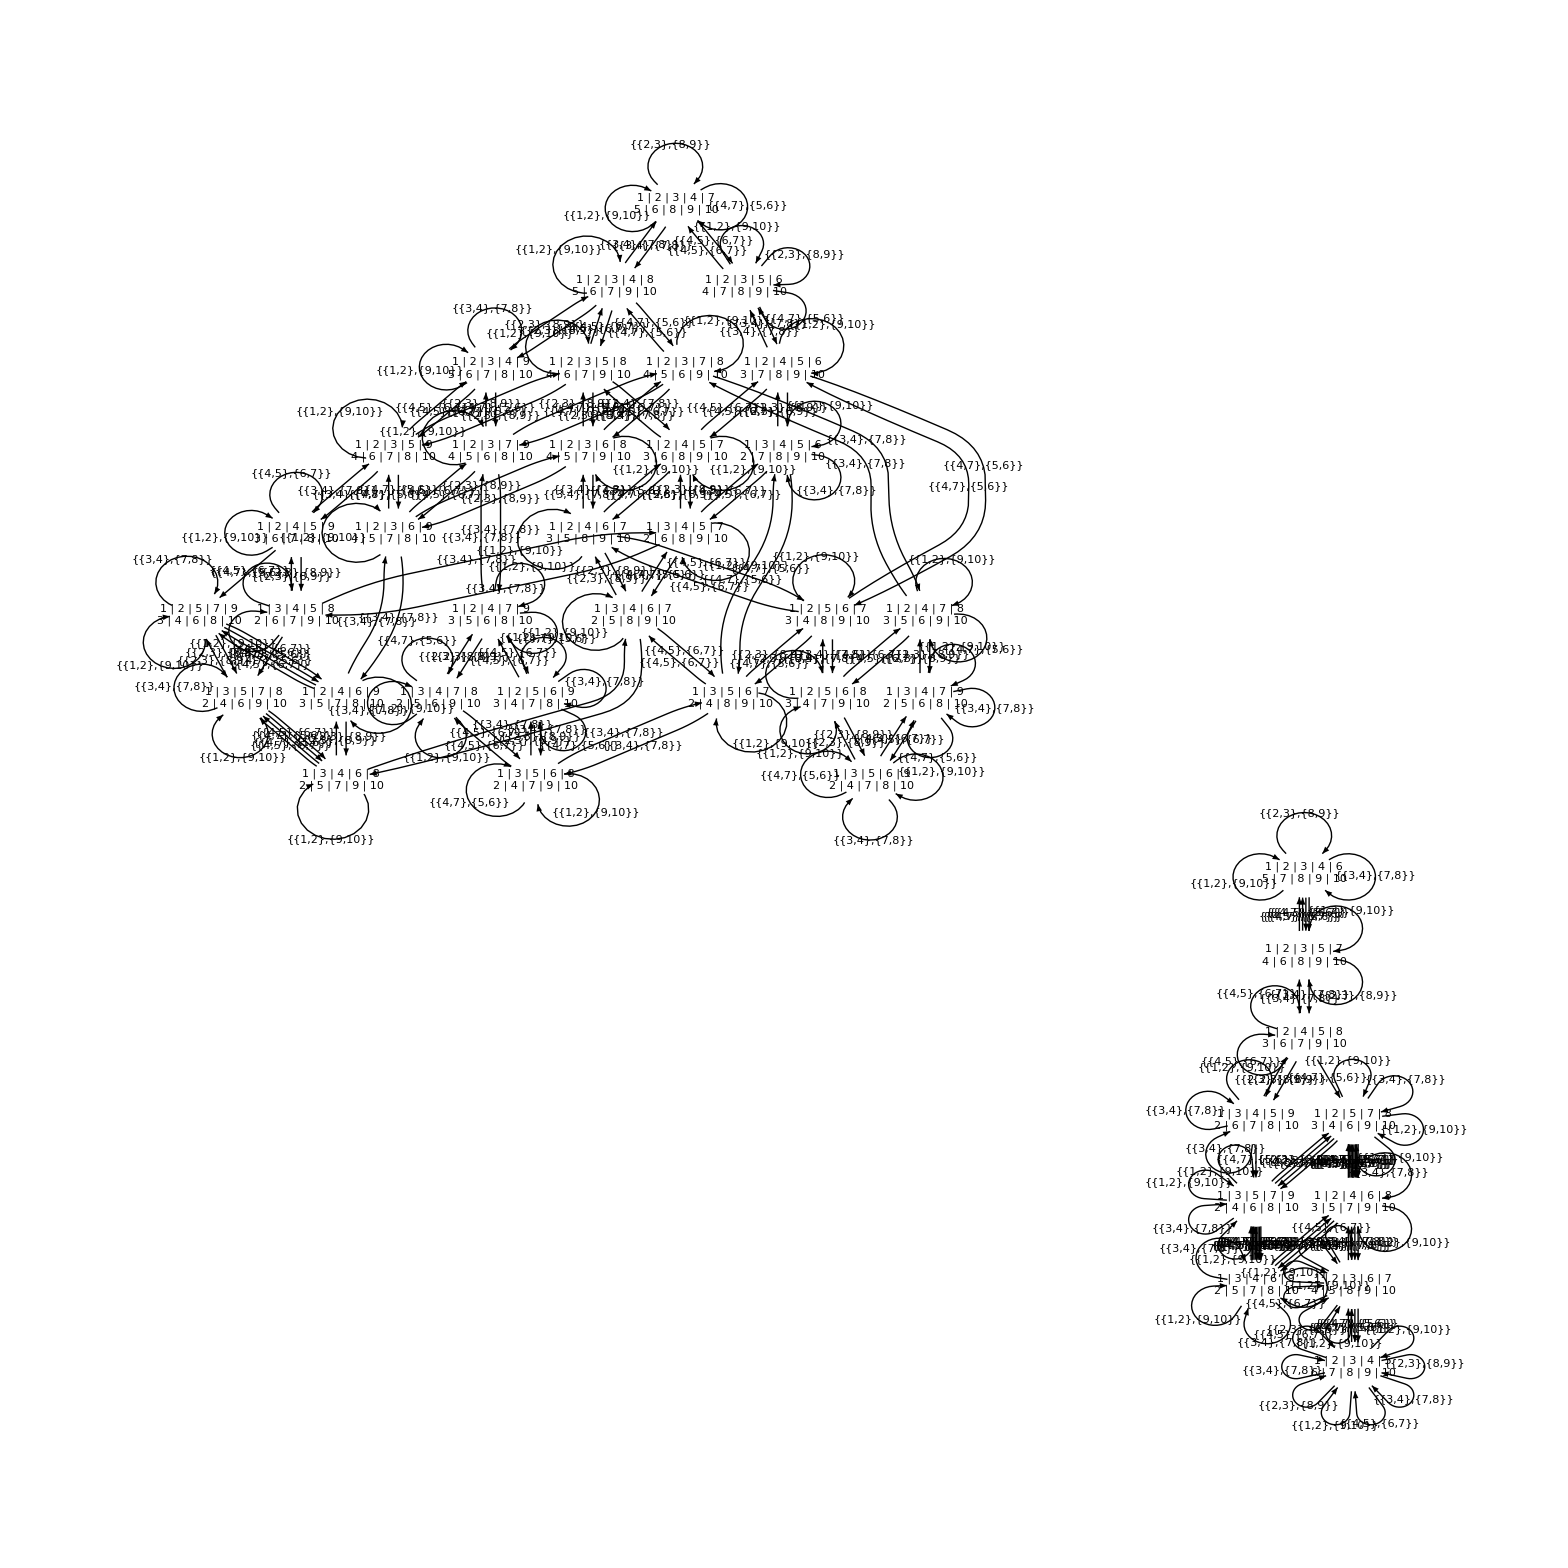

{258.282,Null}

```mathematica
n=5; Timing[findOrbits[YoungTableaux[n,2],DnGenerators[n]]]
```

## Scratch work

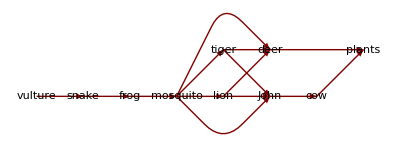

```mathematica
LayeredGraphPlot[{"lion"->"John","tiger"->"John","tiger"->"deer","lion"->"deer","deer"->"plants","mosquito"->"lion","frog"->"mosquito","mosquito"->"tiger","John"->"cow","cow"->"plants","mosquito"->"deer","mosquito"->"John","snake"->"frog","vulture"->"snake"},Left,VertexLabeling->True]
```

```mathematica
n=2;
yd={{1,3,5},{2,4,6}};
Table[YDTPdisplay[YDPerm[yd,Cn[n][[i]]],Cn[n][[i]]],{i,Length[Cn[n]]}]
(* Export["~/YoungTableaux.pdf",%]; *)
```

{-Graphics-
1 | 3 | 5
2 | 4 | 6
{},-Graphics-
1 | 2 | 5
3 | 4 | 6
{{2,3}},-Graphics-
1 | 3 | 5
2 | 4 | 6
{{1,2},{3,4}},-Graphics-
1 | 2 | 5
3 | 4 | 6
{{1,2,4,3}},-Graphics-
1 | 2 | 5
3 | 4 | 6
{{1,3,4,2}},-Graphics-
1 | 3 | 5
2 | 4 | 6
{{1,3},{2,4}},-Graphics-
1 | 2 | 5
3 | 4 | 6
{{1,4}},-Graphics-
1 | 3 | 5
2 | 4 | 6
{{1,4},{2,3}}}